# Defining Functions:

```mathematica
Clear[kx];
Clear[ky];
n1[kx_,ky_]:=-kx*Sqrt[3]/2+(3/2)*ky
n2[kx_,ky_]:=kx*Sqrt[3]/2+(3/2)*ky
gamma0mag[Cp_,Cz_,kx_,ky_]:= Sqrt[(Cz+Cp*(Cos[n1[kx,ky]]+Cos[n2[kx,ky]]))^2 + (Cp*(Sin[n1[kx,ky]]+Sin[n2[kx,ky]]))^2]

gammaZmag[Bp_,Bz_,P1_,P_,K1_,kx_,ky_] := Sqrt[((1+P+K1*(1+P1))*Bz+Bp*K1*(1+P1)*(Cos[n1[kx,ky]]+Cos[n2[kx,ky]]))^2+(Bp*K1*(1+P1)*(Sin[n1[kx,ky]]+Sin[n2[kx,ky]]))^2]

gammaXmag[P1_,K1_,Bp_,Bz_,kx_,ky_] := Sqrt[(Bp((1+K1)*Cos[n1[kx,ky]]+K1*Cos[n2[kx,ky]])+K1*Bz)^2 +(Bp*((1+K1)*Sin[n1[kx,ky]]+K1*Sin[n2[kx,ky]]))^2]

gammaYmag[P1_,K1_,Bp_,Bz_,kx_,ky_] := Sqrt[(Bp((1+K1)*Cos[n2[kx,ky]]+K1*Cos[n1[kx,ky]])+K1*Bz)^2 +(Bp*((1+K1)*Sin[n2[kx,ky]]+K1*Sin[n1[kx,ky]]))^2]

E0[P1_,K1_,P_,M_,Bp_,Bz_,a1_,a2_]:=2*Bp*a1+Bz*a2+M^2/(3K1*(1+P1)+1+P)

gamma0Zmag2[P1_,P_,K1_,Cp_,Cz_,Bp_,Bz_,kx_,ky_] :=(Cz-(1+P+K1*(1+P1))*Bz+(Cp-Bp*K1*(1+P1))*(Cos[n1[kx,ky]]+Cos[n2[kx,ky]]))^2+((Cp-Bp*K1(1+P1))(Sin[n1[kx,ky]]+Sin[n2[kx,ky]]))^2

gammaXYmag2[Bp_,kx_,ky_]:= (Bp(Cos[n1[kx,ky]]-Cos[n2[kx,ky]]))^2+(Bp(Sin[n1[kx,ky]]-Sin[n2[kx,ky]]))^2

eigen1[P1_,P_,K1_,Cp_,Cz_,Bp_,Bz_,M_,L_,kx_,ky_]:= Sqrt[(gamma0mag[Cp,Cz,kx,ky]^2+gammaZmag[Bp,Bz,P1,P,K1,kx,ky] ^2)/2 + (M-L)^2 + 
Sqrt[((gamma0mag[Cp,Cz,kx,ky]^2-gammaZmag[Bp,Bz,P1,P,K1,kx,ky]^2 )/2 )^2+((M-L)^2)*gamma0Zmag2[P1,P,K1,Cp,Cz,Bp,Bz,kx,ky]]];

eigen2[P1_,P_,K1_,Cp_,Cz_,Bp_,Bz_,M_,L_,kx_,ky_]:= Sqrt[(gamma0mag[Cp,Cz,kx,ky]^2+gammaZmag[Bp,Bz,P1,P,K1,kx,ky] ^2)/2 + (M-L)^2 - 
Sqrt[((gamma0mag[Cp,Cz,kx,ky]^2-gammaZmag[Bp,Bz,P1,P,K1,kx,ky]^2 )/2 )^2+((M-L)^2)*gamma0Zmag2[P1,P,K1,Cp,Cz,Bp,Bz,kx,ky]]];

eigen3[P1_,K1_,Bp_,Bz_,L_,kx_,ky_]:=Sqrt[(gammaXmag[P1,K1,Bp,Bz,kx,ky]^2+gammaYmag[P1,K1,Bp,Bz,kx,ky]^2)/2+L^2+
Sqrt[((gammaXmag[P1,K1,Bp,Bz,kx,ky]^2-gammaYmag[P1,K1,Bp,Bz,kx,ky]^2)/2)^2+L^2*gammaXYmag2[Bp,kx,ky]]];

eigen4[P1_,K1_,Bp_,Bz_,L_,kx_,ky_]:=Sqrt[(gammaXmag[P1,K1,Bp,Bz,kx,ky]^2+gammaYmag[P1,K1,Bp,Bz,kx,ky]^2)/2+L^2-
Sqrt[((gammaXmag[P1,K1,Bp,Bz,kx,ky]^2-gammaYmag[P1,K1,Bp,Bz,kx,ky]^2)/2)^2+L^2*gammaXYmag2[Bp,kx,ky]]];

Clear[P1];
Clear[P];
Clear[K1];
Clear[M];
Clear[L];
(*Simplify[Eigensum[P1,P,K1,Cp,Cz,Bp,Bz,M,L,kx,ky]]*)
Eigensum[P1_,P_,K1_,Cp_,Cz_,Bp_,Bz_,M_,L_,kx_,ky_]:=1/(√2)(√2 √(Bp^2+2 Bp^2 K1+2 Bp^2 K1^2+Bz^2 K1^2+L^2+2 Bp^2 K1 (1+K1) Cos[√3 kx]+2 Bp Bz K1 (1+2 K1) Cos[(√3 kx)/2] Cos[(3 ky)/2]-√(Bp^2 (-1+Cos[√3 kx]) (-Bz^2 K1^2-2 L^2+Bz^2 K1^2 Cos[3 ky])))+√2 √(Bp^2+2 Bp^2 K1+2 Bp^2 K1^2+Bz^2 K1^2+L^2+2 Bp^2 K1 (1+K1) Cos[√3 kx]+2 Bp Bz K1 (1+2 K1) Cos[(√3 kx)/2] Cos[(3 ky)/2]+√(Bp^2 (-1+Cos[√3 kx]) (-Bz^2 K1^2-2 L^2+Bz^2 K1^2 Cos[3 ky])))+√(2 (L-M)^2+(Cz+2 Cp Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+(Bz (1+K1+P+K1 P1)+2 Bp K1 (1+P1) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 Cp^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2+4 Bp^2 K1^2 (1+P1)^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2-2 √(1/4 ((Cz+2 Cp Cos[(√3 kx)/2] Cos[(3 ky)/2])^2-(Bz (1+K1+P+K1 P1)+2 Bp K1 (1+P1) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 Cp^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2-4 Bp^2 K1^2 (1+P1)^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2)^2+(L-M)^2 ((Cz-Bz (1+K1+P+K1 P1)+2 (Cp-Bp K1 (1+P1)) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 (Cp-Bp K1 (1+P1))^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2)))+√(2 (L-M)^2+(Cz+2 Cp Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+(Bz (1+K1+P+K1 P1)+2 Bp K1 (1+P1) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 Cp^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2+4 Bp^2 K1^2 (1+P1)^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2+2 √(1/4 ((Cz+2 Cp Cos[(√3 kx)/2] Cos[(3 ky)/2])^2-(Bz (1+K1+P+K1 P1)+2 Bp K1 (1+P1) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 Cp^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2-4 Bp^2 K1^2 (1+P1)^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2)^2+(L-M)^2 ((Cz-Bz (1+K1+P+K1 P1)+2 (Cp-Bp K1 (1+P1)) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 (Cp-Bp K1 (1+P1))^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2))))
E0[P1_,K1_,P_,M_,Bp_,Bz_,a1_,a2_]:=2*Bp*a1+Bz*a2+M^2/(3K1*(1+P1)+1+P)
Energy [P1_,P_,K1_,A1_,A2_,Bp_,Bz_,M_,L_]:= -1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[Eigensum[P1,P,K1,A1,A2,Bp,Bz,M,L,kx,ky],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[Eigensum[P1,P,K1,A1,A2,Bp,Bz,M,L,kx,ky],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[Eigensum[P1,P,K1,A1,A2,Bp,Bz,M,L,kx,ky],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}])+E0[P1,K1,P,M,Bp,Bz,A1,A2]
FBp[kx_,ky_,i_]:=(D[Eigensum[P1,P,K1,cp[[i]],cz[[i]],Bp,bz[[i]],m[[i]]*(3K1*(1+P1)+1+P),l[[i]],kx,ky],Bp]/. Bp->bp[[i]]);
FBz[kx_,ky_,i_]:= (D[Eigensum[P1,P,K1,cp[[i]],cz[[i]],bp[[i]],Bz,m[[i]]*(3K1*(1+P1)+1+P),l[[i]],kx,ky],Bz]/. Bz->bz[[i]]);
FA1[kx_,ky_,i_]:= (D[Eigensum[P1,P,K1, Cp,cz[[i]],bp[[i]],bz[[i]],m[[i]]*(3K1*(1+P1)+1+P),l[[i]],kx,ky],Cp]/. Cp->cp[[i]]);
FA2[kx_,ky_,i_]:=(D[Eigensum[P1,P,K1,cp[[i]], Cz,bp[[i]],bz[[i]],m[[i]]*(3K1*(1+P1)+1+P),l[[i]],kx,ky],Cz]/. Cz->cz[[i]]);
FM[kx_,ky_,i_]:=(D[Eigensum[P1,P,K1,cp[[i]], cz[[i]],bp[[i]],bz[[i]],M,l[[i]],kx,ky],M]/. M->m[[i]]*(3K1*(1+P1)+1+P));
FL[kx_,ky_,P1_,K1_,l_,i_]:=(D[(eigen3[P1,K1,bp[[i]],bz[[i]],L,kx,ky] +eigen4[P1,K1,bp[[i]],bz[[i]],L,kx,ky]),L]/. L->l);
```

```mathematica
Storedvalue2={{1.104552200533518,1.1045531134989053,0.524865355551145,0.5248818126301749,0.,1.1670710287664756*^-17},{1.1044470963390178,1.1045527913251676,0.5248468436652403,0.5248977115425865,0.01,0.01098243811757573},{1.104130344868441,1.1045540319428695,0.524790931318847,0.525007876173319,0.02,0.021968868654881898},{1.103602022280947,1.1045559083411727,0.5246972469640958,0.5251858872060415,0.03,0.03295194740929611},{1.102861866495323,1.1045584687365468,0.5245657719517783,0.525435345179388,0.04,0.04392433629392637},{1.101909842457597,1.1045616011103068,0.524396253034207,0.5257567237040773,0.05,0.05487870225665751},{1.100746098144969,1.1045650742989142,0.5241883771625381,0.5261497934085763,0.06,0.06580773751006658},{1.0993709233464906,1.1045687395816133,0.5239417429496039,0.52661557266277,0.07,0.07670417082254596},{1.0977927428492524,1.104557495539214,0.524106009189931,0.5271458191424478,0.08,0.087636386670767},{1.0959884586778956,1.1045746373840812,0.5233311044852289,0.5277633897040599,0.09,0.09837058508973856},{1.0939823933094386,1.1045763805303728,0.5229660964779215,0.5284461045797442,0.1,0.10912640351209062},{1.0917675832178304,1.1045764779500886,0.5225606049538908,0.5292015099166189,0.11,0.1198213595999696},{1.0893449884286217,1.104574088884823,0.5221136860482967,0.5300296774676145,0.12,0.13044855060038807},{1.086715497665018,1.1045695243257345,0.5216255081587925,0.5309311583209791,0.13,0.1410014826747868},{1.0838805248493177,1.1045615218998228,0.5210935048168015,0.5319058764278501,0.14,0.15147307834212223},{1.0808411550991566,1.1045492076612626,0.5205200692100479,0.5329540044163886,0.15,0.16185780458656515},{1.0775985566531017,1.104531406010187,0.5199013783785853,0.5340756854872158,0.16,0.17214847980484074},{1.0741539686855488,1.1045077300723127,0.5192372300136465,0.5352713910886252,0.17,0.18233911278415088},{1.070508600909825,1.1044768564772212,0.5185266427484195,0.5365413085814537,0.18,0.1924236385116582},{1.0666585403919453,1.1044383532145101,0.5177675673138331,0.5378898584126404,0.19,0.202408732219464},{1.0625930969866173,1.1043934274323222,0.5169559846972022,0.5393166975891631,0.2,0.21231404075282487},{1.0583295419724736,1.104337000084699,0.5160950275453023,0.5408211472660837,0.21,0.22209163721761668},{1.0538703220820222,1.1042677562931373,0.515180874851556,0.5424012560025446,0.22,0.23173206067452284},{1.0492181450986906,1.1041831353877856,0.5142137035885277,0.5440562604543462,0.23,0.24122744062233614},{1.044375400634484,1.1040815619169946,0.5131915180132328,0.5457871962433771,0.24,0.2505699875821848},{1.0393426116765672,1.1039642536185699,0.5121111828741037,0.5475949626949709,0.25,0.2597511861613691},{1.034125879031652,1.1038249798514064,0.5109724076682172,0.5494770974341905,0.26,0.26876434108572295},{1.028725897125349,1.1036621235630923,0.5097724238351026,0.5514345061389802,0.27,0.2776018147229095},{1.0231449448043222,1.1034726378862403,0.5085092456287316,0.5534669406253782,0.28,0.2862566200655076},{1.0173850907920667,1.1032533739847594,0.5071800791741898,0.5555745017133088,0.29000000000000004,0.2947215511492913},{1.0113641910615556,1.103018414296406,0.5057659663062245,0.5577963489971353,0.30000000000000004,0.30310586252942345},{1.0049917949671086,1.1027642982784642,0.5042480953930486,0.5601703400059971,0.31,0.31150369592363975},{0.9983866846334406,1.102483288342148,0.5026411995990319,0.5626500863594508,0.32,0.3197253330763585},{0.9915727336975718,1.1021549493051117,0.5009480031986212,0.5652218993415831,0.33,0.32773388052118374},{0.9846125728528771,1.1017924058225694,0.49917063193507083,0.5678679772739149,0.34,0.3354435608112433},{0.9775220112696559,1.1013607860504362,0.4973137507737038,0.5705713560074617,0.35000000000000003,0.34284180500474243},{0.9703195497624715,1.1008647425993425,0.4953740347408949,0.5733280461021885,0.36,0.3499094106933364},{0.9630217383231888,1.1003012510946726,0.49334945618022624,0.576132018296312,0.37,0.3566344744949575},{0.9556361013400817,1.0996295308726742,0.49124438789135333,0.5789665412685051,0.38,0.3630160193702943},{0.9481687093212186,1.0988796689663756,0.48904685035085327,0.5818418688449031,0.39,0.36904673329750776},{0.9406211424145952,1.098030627228709,0.48675565837225365,0.5847507271859412,0.4,0.37473111770511097},{0.9329867288846286,1.0970742928070665,0.4843632640061431,0.587695225688934,0.41000000000000003,0.3800720905194637},{0.9252606669799586,1.0960030816217514,0.4818636820460708,0.5906765886541042,0.42000000000000004,0.3850757832856878},{0.9174173565596874,1.0948084744292979,0.4792430927650804,0.5937047633639861,0.43000000000000005,0.3897434149561423},{0.9094519632494967,1.093344439775825,0.4764944311047491,0.5967830170293023,0.44000000000000006,0.39408181088695055},{0.9013292679120037,1.0920156433123727,0.4735963485628369,0.5999229934947701,0.45,0.39808621301739777},{0.893516861558814,1.0903319146536237,0.4706726730989537,0.6028811978330064,0.46,0.40151970010327326},{0.8859829435781413,1.0884232604493753,0.4677149857892202,0.6056631487176903,0.47000000000000003,0.4044365341577651},{0.878153223568095,1.0863527679787888,0.46455515036932443,0.6085671350573241,0.48,0.40709798285305976},{0.8700091474110556,1.0841069464032436,0.46117362398722106,0.6116029462956017,0.49,0.40949703271846993},{0.8614354363527192,1.0816713978086276,0.4575167587372773,0.6148295586277956,0.5,0.4115985335248741},{0.8523631700346345,1.0790269244851178,0.4535384421575864,0.6182846948573122,0.51,0.4133658617338972},{0.842687926672072,1.0761471588937257,0.4491730510415595,0.6220244620531508,0.52,0.4147385426086941},{0.8322940279293563,1.0729946984245884,0.4443397542502052,0.6261117169919757,0.53,0.41562818841523913},{0.8210535790548986,1.0695128856526719,0.43893665181518565,0.6306147328671549,0.54,0.41590035913948165},{0.8088834729744171,1.0656156719106642,0.4328581618580109,0.6355736785330192,0.55,0.4153609139983927},{0.7958942423939281,1.0611736162335488,0.4260554442167296,0.6409105696345438,0.56,0.4137566136687779},{0.7827014136376624,1.056014336239264,0.41869776201170816,0.6462345129907907,0.5700000000000001,0.4108529828355569},{0.7699333518804244,1.0502536946092431,0.41301283735107264,0.6486988886665396,0.5800000000000001,0.4088265521702891},{0.7481602296541305,1.0472110016004754,0.40446432678796407,0.658668441677664,0.5900000000000001,0.3993418746334669},{0.7601841616514401,1.036769232616673,0.40256376839498986,0.6513148762090573,0.6,0.4001867251149785},{0.7532514016272172,1.0295517082962213,0.3971390637710888,0.6523943555759697,0.6100000000000001,0.3966589712233191},{0.7434704544660135,1.0216864897527567,0.3899042028484459,0.6550665353683628,0.62,0.3924256310520503},{0.7304053219407146,1.0131863813504403,0.3805821583565386,0.6596139769724602,0.63,0.38737796395440655},{0.7136786780585388,1.0038307649310725,0.3685644424024059,0.6663810074108537,0.64,0.3811809492785545},{0.6926562683450149,0.9932867718927273,0.35295725830898206,0.6759253141624407,0.65,0.3732216064246971},{0.6690549275553261,0.9810685372557472,0.3340725586732546,0.6872005770197169,0.66,0.3630312130582941},{0.6529903863863884,0.9705056585386969,0.3216114389941553,0.6919776583796404,0.67,0.3566202757704672},{0.6424228624561309,0.9608982600906237,0.31379796124973053,0.6923396761335553,0.68,0.3529484368904589},{0.6352613004262608,0.95125711093717,0.30849611625257733,0.6901052531300349,0.69,0.35059098077441375},{0.6310651483384209,0.941263149923719,0.3046663460976608,0.6861503877581988,0.7,0.34851980543255934},{0.6245505188184883,0.931446411934166,0.3003123139875212,0.6827201731213092,0.71,0.346835685684902},{0.6170455990539423,0.921433465356701,0.29532415989055305,0.6794990689312469,0.72,0.34498867764111263},{0.6086867217711494,0.911356472022397,0.2900349562926906,0.6763075118057702,0.73,0.34321869309095787},{0.5996433125245504,0.9012123646146091,0.28453640930695645,0.673050809954214,0.74,0.3415558852524614},{0.5932893204746839,0.8905704783899352,0.28057215900387006,0.6681036900204592,0.75,0.3403810571253275},{0.5806325647893498,0.8805954533086046,0.2734713248264908,0.6657882770156806,0.76,0.3386668723826598},{0.5677033254239976,0.8705666513175008,0.26638273949160396,0.6631581463320085,0.77,0.337137389484383},{0.554479354587309,0.8604725890060637,0.25928156577243716,0.6602268315253879,0.78,0.3357760726337667},{0.5409397170509221,0.8503034191746969,0.25214626896310216,0.6570039182930403,0.79,0.3345695350803561},{0.5270597984588467,0.8400506683745639,0.24495545487015427,0.6534974956545958,0.8,0.33350636072571327},{0.5128100503897572,0.82970708533305,0.2376868868630459,0.6497148321642544,0.81,0.33257667572049165},{0.4981578756260661,0.8192660745181781,0.23031813878458832,0.6456614951901256,0.8200000000000001,0.33177199202345364},{0.48306494688130386,0.8087217642148973,0.22282508899843326,0.6413423347494168,0.83,0.3310848638859126},{0.4674870110997027,0.7980686887616965,0.21518166596909846,0.6367611698588219,0.84,0.33050871393219255},{0.45137193759686595,0.7873017925234594,0.20735887151127158,0.6319211666523314,0.85,0.33003775604197416},{0.43465817956084785,0.776416254149136,0.19932393378132787,0.6268246955435788,0.86,0.3296668123820304},{0.4172719615693455,0.7654074597233029,0.19103897663920125,0.6214734837425191,0.87,0.3293913022199139},{0.39912350309755174,0.7542709319439602,0.18245923993301383,0.6158686673858408,0.88,0.32920715735021455},{0.3801016081581942,0.7430023519311387,0.17353057808381434,0.6100108782449827,0.89,0.32911083680727626},{0.3600658877182457,0.7315973913896656,0.1641859313996544,0.6039001988635823,0.9,0.3290994352239018},{0.33883496972524246,0.7200515869835189,0.1543400056745153,0.5975360668205169,0.91,0.3291709553902801},{0.31616644895341706,0.7083600990394331,0.1438802454579306,0.5909172621110862,0.92,0.32932490508419254},{0.29172482804502053,0.6965163478597179,0.13265261414431162,0.5840407735007819,0.9299999999999999,0.32956409582760665},{0.2650225489259649,0.6845067115611945,0.12043533854869919,0.5768975531209902,0.94,0.3298986898717449},{0.235302896668824,0.672286586866823,0.1068866206413957,0.5694524415960414,0.95,0.33035564274858176},{0.20127210532734455,0.6596509573358904,0.09142015894045052,0.5615317545215062,0.96,0.3309802816483834},{0.16023638884324182,0.6453689177512238,0.07275431671486773,0.5520426368182277,0.97,0.3314433113535699},{0.10046458813341515,0.6237881680748887,0.044897168899743024,0.5355072079337226,0.98,0.32347827106611643},{0.001868772112404979,0.8158141553417618,0.0010945147784271565,0.7160019152891988,0.99,0.5025259425149989}};
```

```mathematica
test =30;
Storedvalue2[[test]]
cpi=Storedvalue2[[test]][[1]];
czi=Storedvalue2[[test]][[2]];
bpi=Storedvalue2[[test]][[3]];
bzi=Storedvalue2[[test]][[4]];
li=Storedvalue2[[test]][[6]];
```

{0.877731,0.575093,0.260085,0.23023,0.87,0.742848}

```mathematica
cpi=1.1045531134878759;
czi=1.1045531134878759;
bpi=0.5248653556502452;
bzi=0.5248818124310457;
li=0;
```

# Starting investigation:

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

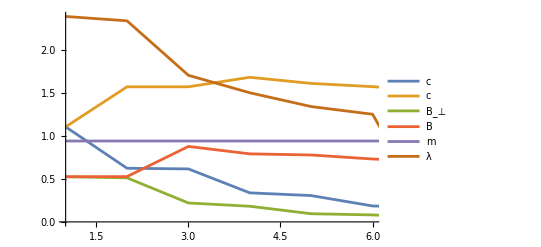

Final MFT Parameters:c_⊥ =0.185227, c_z=1.57176, B_⊥=0.0810255TraditionalForm`0.7309, M=2.632, m=0.94, λ=1.25098

```mathematica
loop=90;
Clear[cp];
Clear[cz];


cp= ConstantArray[cpi,loop];
cz = ConstantArray[czi,loop];
bp=ConstantArray[bpi,loop];
bz=ConstantArray[bzi,loop];
m=ConstantArray[0.94,loop];
l=ConstantArray[0,loop];
P1=0;
P=0;
K1=0.6;
For[i=1,i<loop,i++,

(*Lagrangian multiplier*)
Clear[l1];
Clear[m2];
l1=Range[0,3,0.01];
l1b = Range[3,10,0.1];
l1c = Range[11,100,1];
l1d = Range[100,9750,50];
l1e=Range[1000,10000,100];
(*l1 = Join[l1a,l1b,l1c,l1d];*);
m2 = ConstantArray[10,Length[l1]];
For[j=1,j<=Length[l1],j++,
m2[[j]] =(1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))*(NIntegrate[FL[kx,ky,P1,K1,l1[[j]],i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FL[kx,ky,P1,K1,l1[[j]],i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FL[kx,ky,P1,K1,l1[[j]],i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);
];

g=Interpolation[Transpose[{l1,m2}]];

l[[i]]=InverseFunction[g][m[[i]]] (*this is unscaled magnetisation*);
final=i;

(*other MFT variables*)
cp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FBp[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FBp [kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FBp[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

cz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FBz[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FBz[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+
NIntegrate[FBz[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

bp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FA1[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FA1[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FA1[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

bz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FA2[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FA2[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FA2[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

];



ListLinePlot[{cp,cz,bp,bz,m,l},PlotLegends->{"c","c","B_⊥","B","m","λ"},PlotRange->{{1,final},Automatic}]
Print["Final MFT Parameters:","c_⊥ =",cp[[final]] ,", c_z=",cz[[final]],", B_⊥=", bp[[final]],"TraditionalForm`", bz[[final]], ", M=", m[[final]]*(3K1*(1+P1)+1+P),", m=", m[[final]], ", λ=", l[[final]]]
z=final-1;
(*Print["Penultimate MFT Parameters:","c_⊥ =",cp[[z]] ,", c_z=",cz[[z]] ,", B_⊥=", bp[[z]],"TraditionalForm`", bz[[z]], ", M=", m[[z]]*(3K1*(1+P1)+1+P),", m=", m[[z]], ", λ=", l[[z]]]*)
```

Note there is an error of 10^(-7)

-2.80007

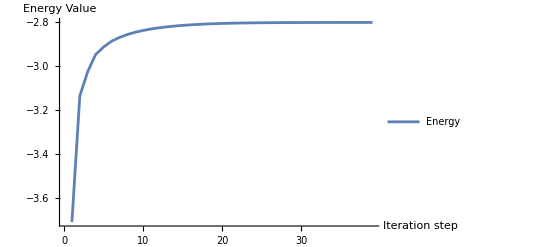

```mathematica
Energyval=ConstantArray[0,final-1];
For[n=2,n<=final,n++,
Energyval[[n-1]] = Energy [P1,P,K1,cp[[n]],cz[[n]],bp[[n]],bz[[n]], m[[n]]*(3K1*(1+P1)+1+P),l[[n]]]
]
ListLinePlot[Energyval,PlotRange->Full,PlotLegends->{"Energy"}, AxesLabel->{"Iteration step", "Energy Value"}, PlotRange->{10,20}]
Print[ Energyval[[final-1]]]
```

#### Example Plot of the Lagrange multiplier

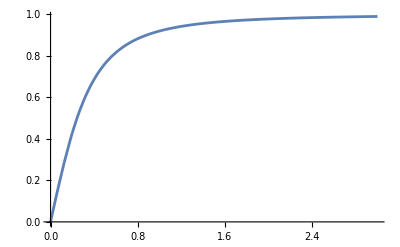

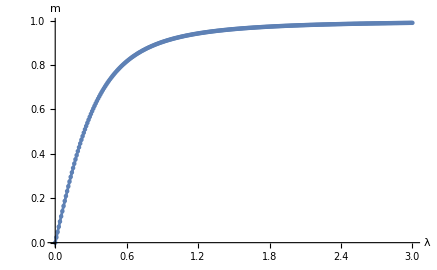

```mathematica
Plot1= Plot[g[x],{x,0,3},PlotRange->Full]
```